# Caminatas cuánticas

## Importando cosas

```mathematica
Get[NotebookDirectory[]<>"../AmadoTemp/DTQW.wl"]
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
<<MaTeX`
```

Get::noopen: Cannot open MaTeX`.

$Failed

## Definiendo variables

```mathematica
IndigoC=RGBColor["#729cfc"];
AquaC=RGBColor["#4bd7e5"];
DeepBlueC=RGBColor["#1e2c88"];
```

```mathematica
qlabels=Import[NotebookDirectory[]<>#,{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]]&/@{"Labels_pos.pdf","Labels_prob.pdf"};
clabels=Import[NotebookDirectory[]<>#,{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]]&/@{"Labels_pos.pdf","Labels_probc.pdf"};
plotargs={
BaseStyle->{FontFamily->"LM Roman 12",FontSize->15},
PlotRange->All,
Axes->False,
Frame->True,
Mesh->All,
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,Opacity[0.5]]
};
```

```mathematica
TeXLabel[tlist_List]:=MaTeX[
"\\begin{gathered}\n"<>Fold[
StringJoin[#1,"\\\\\n",#2]&,ToString@StringForm["\\text{``}",#]&/@tlist
]<>"\n\\end{gathered}",
FontSize->14,
Magnification->1.3,
"Preamble"->{"\\usepackage{physics}"}
]
```

## Inicializaciones

```mathematica
InitializeDTQW[2,401]
MakeCoin[1/2,0,0];
MakeShift[];
MakeUnitary[];
```

```mathematica
plotlist={};
```

## Estado puro aleatorio de un cúbit

```mathematica
{θ,ϕ}={RandomReal[{0,π}],RandomReal[{0,2π}]}
```

{0.451227,0.23907}

```mathematica
psialeatorio=VectorState[{{Sin[θ/2],1,0},{Cos[θ/2]*Exp[ⅈ ϕ],0,0}}];
```

## Verificar si existe una distribución límite o si se hace infinitamente ancha

### Sin decoherencia

```mathematica
Range[20,20+30 (7-1),30]
```

{20,50,80,110,140,170,200}

```mathematica
rhofvariost=(#.#†&@DTQW2[psialeatorio,#])&/@Range[20,20+30 (7-1),30]
```

```mathematica
probsvariost=(Abs@Diagonal@MatrixPartialTrace[#,1,{2,401}])&/@rhofvariost;
```

```mathematica
Total/@probsvariost
```

{1.,1.,1.,1.,1.,1.,1.}

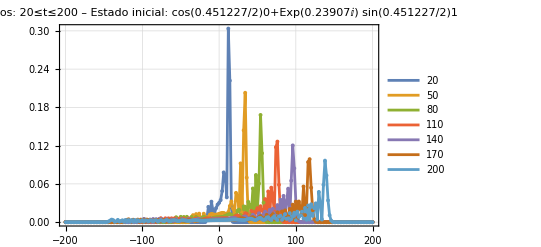

```mathematica
plotvariost=ListLinePlot[Evaluate@Table[{Range[-200,200,2],probs[[;;;;2]]}ᵀ,{probs,probsvariost}],
plotargs,
PlotLabel->StringForm["Pasos: 20≤t≤200 – Estado inicial: cos(``/2)0+Exp(``ⅈ) sin(``/2)1",θ,ϕ,θ],
PlotLegends->Range[20,20+30 (7-1),30],
ImageSize->Scaled[0.75]]
AppendTo[plotlist,ToString@Unevaluated@plotvariost];
```

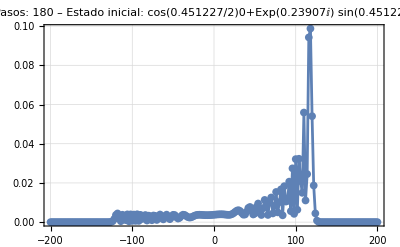

```mathematica
ListLinePlot[{Range[-200,200,2],probsvariost[[-2]][[;;;;2]]}ᵀ,
plotargs,
PlotLabel->StringForm["Pasos: 180 – Estado inicial: cos(``/2)0+Exp(``ⅈ) sin(``/2)1",θ,ϕ,θ],
ImageSize->Scaled[0.75]]
```

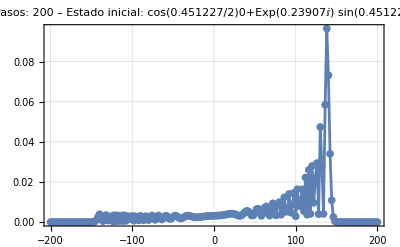

```mathematica
ListLinePlot[{Range[-200,200,2],probsvariost[[-1]][[;;;;2]]}ᵀ,
plotargs,
PlotLabel->StringForm["Pasos: 200 – Estado inicial: cos(``/2)0+Exp(``ⅈ) sin(``/2)1",θ,ϕ,θ],
ImageSize->Scaled[0.75]]
```

### Con decoherencia

```mathematica
rhofvariostwd=(DTQW2wDecoherence[psialeatorio,0.5,#])&/@Range[20,20+30 (7-1),30];
```

```mathematica
probsvariostwd=(Abs@Diagonal@MatrixPartialTrace[#,1,{2,401}])&/@rhofvariostwd;
```

```mathematica
Total/@probsvariostwd
```

{1.,1.,1.,1.,1.,1.,1.}

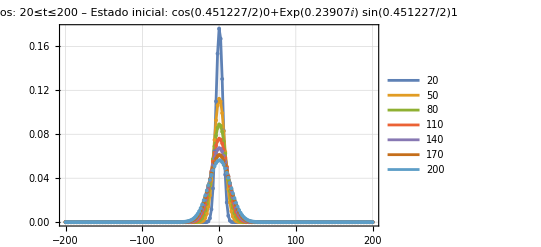

```mathematica
plotvariostwd=ListLinePlot[Evaluate@Table[{Range[-200,200,2],probs[[;;;;2]]}ᵀ,{probs,probsvariostwd}],
plotargs,
PlotLabel->StringForm["Pasos: 20≤t≤200 – Estado inicial: cos(``/2)0+Exp(``ⅈ) sin(``/2)1",θ,ϕ,θ],
PlotLegends->Range[20,20+30 (7-1),30],
ImageSize->Scaled[0.75]]
AppendTo[plotlist,ToString@Unevaluated@plotvariostwd];
```

## Verificar en qué t se igualan la RW con la DTQW con p=0.5

```mathematica
PascalRow[n_Integer]:=Riffle[Binomial[n,#]/(2^n)&@Range[0,n],0]
RandomWalkDistribution[n_Integer]:=Transpose[{Range[-n,n],PascalRow[n]}]
```

### 20 pasos

```mathematica
ListLinePlot[{{Range[-200,200,2],probsvariostwd[[1]][[;;;;2]]}ᵀ,{Range[-20,20,2],PascalRow[20][[;;;;2]]}ᵀ},
DeleteCases[plotargs,HoldPattern[PlotRange->_]],
PlotLabel->StringForm["Pasos: 20 – Estado inicial: cos(``/2)0+Exp(``ⅈ) sin(``/2)1",θ,ϕ,θ],
PlotStyle->{Directive[IndigoC,Dashed],Directive[AquaC,Dashed]},
PlotLegends->{"DTQW","RW"},
PlotRange->{{-20,20},All},
ImageSize->Scaled[0.75],
PlotMarkers->{"●", "■", "◆", "▲", "▼", "○", "□", "◇"}]
```

-Graphics-

```mathematica
difference20=Abs[PascalRow[20]-probsvariostwd[[1,201-20;;201+20]]]
```

{4.04041×10^-7,0,7.27274×10^-6,0,0.0000614142,0,0.000322425,0,0.00117455,0,0.00313213,0,0.00626425,0,0.00939638,0,0.0101794,0,0.00678627,0,0.,0,0.00678627,0,0.0101794,0,0.00939638,0,0.00626425,0,0.00313213,0,0.00117455,0,0.000322425,0,0.0000614142,0,7.27274×10^-6,0,4.04041×10^-7}

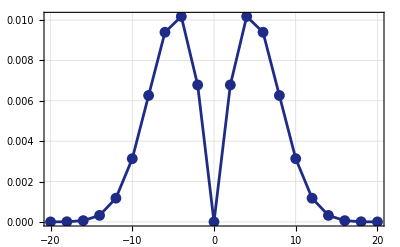

```mathematica
ListLinePlot[{Range[-20,20,2],difference20[[;;;;2]]}ᵀ,
plotargs,
PlotStyle->DeepBlueC,
ImageSize->Scaled[0.75],
Mesh->All]
```

### 50 pasos

```mathematica
ListLinePlot[{{Range[-200,200,2],probsvariostwd[[2]][[;;;;2]]}ᵀ,{Range[-50,50,2],PascalRow[50][[;;;;2]]}ᵀ},
DeleteCases[plotargs,HoldPattern[PlotRange->_]],
PlotLabel->StringForm["Pasos: 50 – Estado inicial: cos(``/2)0+Exp(``ⅈ) sin(``/2)1",θ,ϕ,θ],
PlotStyle->{Directive[IndigoC,Dashed],Directive[AquaC,Dashed]},
PlotRange->{{-50,50},All},
ImageSize->Scaled[0.75],
PlotMarkers->{"●", "■", "◆", "▲", "▼", "○", "□", "◇"}]
```

-Graphics-

```mathematica
difference50=Abs[PascalRow[50]-probsvariostwd[[2,201-50;;201+50]]];
```

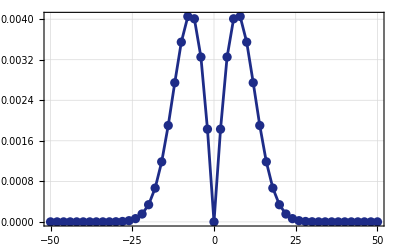

```mathematica
ListLinePlot[{Range[-50,50,2],difference50[[;;;;2]]}ᵀ,
plotargs,
PlotStyle->DeepBlueC,
ImageSize->Scaled[0.75],
Mesh->All]
```

### 80 pasos

```mathematica
ListLinePlot[{{Range[-200,200,2],probsvariostwd[[3]][[;;;;2]]}ᵀ,{Range[-80,80,2],PascalRow[80][[;;;;2]]}ᵀ},
DeleteCases[plotargs,HoldPattern[PlotRange->_]],
PlotLabel->StringForm["Pasos: 80 – Estado inicial: cos(``/2)0+Exp(``ⅈ) sin(``/2)1",θ,ϕ,θ],
PlotStyle->{Directive[IndigoC,Dashed],Directive[AquaC,Dashed]},
PlotRange->{{-80,80},All},
ImageSize->Scaled[0.75],
PlotMarkers->{"●", "■", "◆", "▲", "▼", "○", "□", "◇"}]
```

-Graphics-

```mathematica
difference80=Abs[PascalRow[80]-probsvariostwd[[3,201-80;;201+80]]];
```

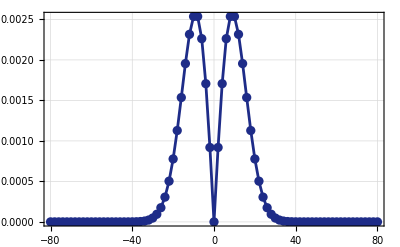

```mathematica
ListLinePlot[{Range[-80,80,2],difference80[[;;;;2]]}ᵀ,
plotargs,
PlotStyle->DeepBlueC,
ImageSize->Scaled[0.75],
Mesh->All]
```

### 110 pasos

```mathematica
ListLinePlot[{{Range[-200,200,2],probsvariostwd[[4]][[;;;;2]]}ᵀ,{Range[-110,110,2],PascalRow[110][[;;;;2]]}ᵀ},
DeleteCases[plotargs,HoldPattern[PlotRange->_]],
PlotLabel->StringForm["Pasos: 110 – Estado inicial: cos(``/2)0+Exp(``ⅈ) sin(``/2)1",θ,ϕ,θ],
PlotStyle->{Directive[IndigoC,Dashed],Directive[AquaC,Dashed]},
PlotRange->{{-110,110},All},
ImageSize->Scaled[0.75],
PlotMarkers->{"●", "■", "◆", "▲", "▼", "○", "□", "◇"}]
```

-Graphics-

```mathematica
difference110=Abs[PascalRow[110]-probsvariostwd[[4,201-110;;201+110]]];
```

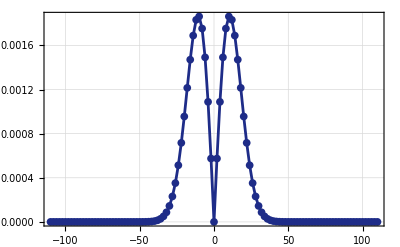

```mathematica
ListLinePlot[{Range[-110,110,2],difference110[[;;;;2]]}ᵀ,
plotargs,
PlotStyle->DeepBlueC,
ImageSize->Scaled[0.75],
Mesh->All]
```

### 140 pasos

```mathematica
ListLinePlot[{{Range[-200,200,2],probsvariostwd[[5]][[;;;;2]]}ᵀ,{Range[-140,140,2],PascalRow[140][[;;;;2]]}ᵀ},
DeleteCases[plotargs,HoldPattern[PlotRange->_]],
PlotLabel->StringForm["Pasos: 140 – Estado inicial: cos(``/2)0+Exp(``ⅈ) sin(``/2)1",θ,ϕ,θ],
PlotStyle->{Directive[IndigoC,Dashed],Directive[AquaC,Dashed]},
PlotRange->{{-140,140},All},
ImageSize->Scaled[0.75],
PlotMarkers->{"●", "■", "◆", "▲", "▼", "○", "□", "◇"}]
```

-Graphics-

```mathematica
difference140=Abs[PascalRow[140]-probsvariostwd[[5,201-140;;201+140]]];
```

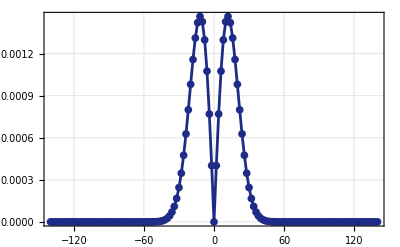

```mathematica
ListLinePlot[{Range[-140,140,2],difference140[[;;;;2]]}ᵀ,
plotargs,
PlotStyle->DeepBlueC,
ImageSize->Scaled[0.75],
Mesh->All]
```

### 170 pasos

```mathematica
ListLinePlot[{{Range[-200,200,2],probsvariostwd[[6]][[;;;;2]]}ᵀ,{Range[-170,170,2],PascalRow[170][[;;;;2]]}ᵀ},
DeleteCases[plotargs,HoldPattern[PlotRange->_]],
PlotLabel->StringForm["Pasos: 170 – Estado inicial: cos(``/2)0+Exp(``ⅈ) sin(``/2)1",θ,ϕ,θ],
PlotStyle->{Directive[IndigoC,Dashed],Directive[AquaC,Dashed]},
PlotRange->{{-170,170},All},
ImageSize->Scaled[0.75],
PlotMarkers->{"●", "■", "◆", "▲", "▼", "○", "□", "◇"}]
```

-Graphics-

### 200 pasos

```mathematica
ListLinePlot[{{Range[-200,200,2],probsvariostwd[[7]][[;;;;2]]}ᵀ,{Range[-200,200,2],PascalRow[200][[;;;;2]]}ᵀ},
DeleteCases[plotargs,HoldPattern[PlotRange->_]],
PlotLabel->StringForm["Pasos: 200 – Estado inicial: cos(``/2)0+Exp(``ⅈ) sin(``/2)1",θ,ϕ,θ],
PlotStyle->{Directive[IndigoC,Dashed],Directive[AquaC,Dashed]},
PlotRange->{{-200,200},All},
ImageSize->Scaled[0.75],
PlotMarkers->{"●", "■", "◆", "▲", "▼", "○", "□", "◇"}]
```

-Graphics-

```mathematica
difference200=Abs[PascalRow[200]-probsvariostwd[[7,201-200;;201+200]]];
```

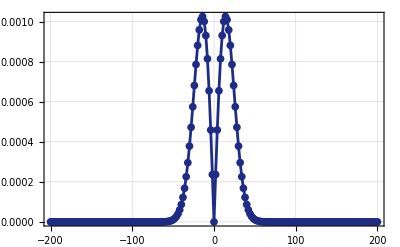

```mathematica
ListLinePlot[{Range[-200,200,2],difference200[[;;;;2]]}ᵀ,
plotargs,
PlotStyle->DeepBlueC,
ImageSize->Scaled[0.75],
Mesh->All]
```